```mathematica
ParamValsForPlotting={hc->0.04,wc->0.0125,hw->0.02,ww->0.00625};
```

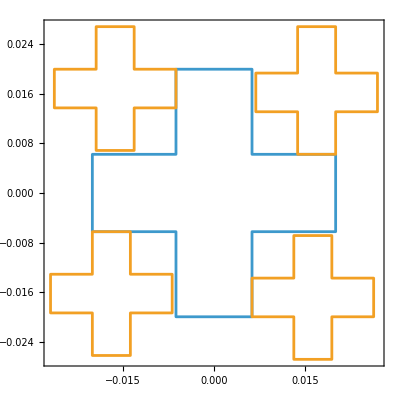

```mathematica
RegCore=Polygon[{
{-wc/2,hc/2 },
{-wc/2, 0.15625hc}, 
{-1.6wc, 0.15625hc}, 
{-1.6wc, -0.15625hc}, 
{-wc/2, -0.15625hc}, 
{-wc/2, -hc/2}, 
{wc/2, -hc/2 }, 
{wc/2, -0.15625hc}, 
{1.6wc, -0.15625hc},
{1.6wc, 0.15625hc}, 
{wc/2, 0.15625hc }, 
{wc/2, hc/2}, 
{-wc/2, hc/2}
}];

RegWing =RegionUnion[
Polygon[{
{-ww, hw}, 
{-2.1ww, hw}, 
{-2.1ww, 1.34375hw}, 
{-3.1ww, 1.34375hw}, 
{-3.1ww, hw}, 
{-4.2ww, hw}, 
{-4.2ww, 0.6875hw}, 
{-3.1ww, 0.6875hw}, 
{-3.1ww, 0.34375hw}, 
{-2.1ww, 0.34375hw}, 
{-2.1ww, 0.6875hw}, 
{-ww, 0.6875hw}, 
{-ww, hw}
}],
Polygon[{
{-3.2ww, -0.3125hw}, 
{-3.2ww, -0.65625hw}, 
{-4.3ww, -0.65625hw}, 
{-4.3ww, -0.96875hw}, 
{-3.2ww, -0.96875hw}, 
{-3.2ww, -1.3125hw}, 
{-2.2ww, -1.3125hw}, 
{-2.2ww, -0.96875hw}, 
{-1.1ww, -0.96875hw}, 
{-1.1ww, -0.65625hw}, 
{-2.2ww, -0.65625hw}, 
{-2.2ww, -0.3125hw}, 
{-3.2ww, -0.3125hw}
}],
Polygon[{
{ww, -hw}, 
{2.1ww, -hw}, 
{2.1ww, -1.34375hw}, 
{3.1ww, -1.34375hw}, 
{3.1ww, -hw}, 
{4.2ww, -hw}, 
{4.2ww, -0.6875hw}, 
{3.1ww, -0.6875hw}, 
{3.1ww, -0.34375hw}, 
{2.1ww, -0.34375hw}, 
{2.1ww, -0.6875hw}, 
{ww, -0.6875hw}, 
{ww, -hw}
}],
Polygon[{
{3.2ww, 0.3125hw}, 
{3.2ww, 0.65625hw}, 
{4.3ww, 0.65625hw}, 
{4.3ww, 0.96875hw}, 
{3.2ww, 0.96875hw}, 
{3.2ww, 1.34375hw}, 
{2.2ww, 1.34375hw}, 
{2.2ww, 0.96875hw}, 
{1.1ww, 0.96875hw}, 
{1.1ww,  0.65625hw}, 
{2.2ww,  0.65625hw}, 
{2.2ww, 0.3125hw}, 
{3.2ww, 0.3125hw}
}]
];

RegionPlot[{RegCore/.ParamValsForPlotting,RegWing/.ParamValsForPlotting},AspectRatio->Automatic,PlotStyle->None]
```

```mathematica
×10^-11
```

3.38336×10^-10